```mathematica
DrawIsoLines [debit_ , coordinates_,xminlim_,xmaxlim_,yminlim_,ymaxlim_,phiCount_,psiCount_] := Module [
{we= debit,
coords = coordinates,
xminl=xminlim,
xmaxl=xmaxlim,
yminl=yminlim,
ymaxl=ymaxlim,
phiC=phiCount,
psiC=psiCount,
phi,psi,w,g1,g2},
w[z_]=0;
For[i=1,i<=Length[we],i++,w[z_]=w[z]+we[[i]]/(2π)*Log[z-(coords[[i,1]]+I*coords[[i,2]])]];
phi[z_]=Re[w[z]];
psi[z_]=Im[w[z]];
g1=ContourPlot[phi[x+I*y],{x,xminl,xmaxl},{y,yminl,ymaxl},PlotLegends->Automatic, Contours->phiC,ContourShading->None,AspectRatio->Automatic];
g2=ContourPlot[psi[x+I*y],{x,xminl,xmaxl},{y,yminl,ymaxl},PlotLegends->Automatic, Contours->psiC,ContourShading->None,AspectRatio->Automatic];
Show[g1,g2 ,Graphics[{Thick, Red,Line[{{-10,-10},{10,10}}],Line[{{-10,0},{10,0}}]}]] ];

Coords[i_]={Cos[Pi*(22.5+(i-1)*45)/180],Sin[Pi*(22.5+(i-1)*45)/180]};
```

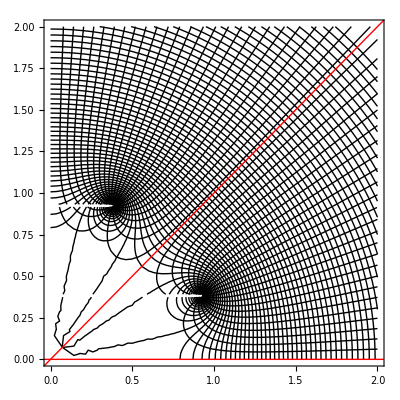

```mathematica
DrawIsoLines[{1,1,1,1,1,1,1,1},
{Coords[1],Coords[2],Coords[3],Coords[4],Coords[5],Coords[6],Coords[7],Coords[8]},0,2,0,2,70,50]
```